# Compute the integral for each element of the sum

NB! Note that for M=0 Ξ1 = 0, and for N=0 Ξ2=0. So should be wrapped in a If[M>0, Ξ1, 0] etc.
NB! Be careful with which definition of Ξ has been used, i.e. whether alpha factors are included or not.

Here P = lim (q -> 0) L q' / sqrt (2 α) = beta/(alpha √α)	 (epsilon0_ (n, αB) - epsilon0_ (m, αB)) = beta/alpha^(5/2) (epsilon_n - epsilon_m)
where epsilon0_ (n, αB) is the dimless energy solution to the untilted case .

Note also that the chirality s has not been implemented

## Setup

```mathematica
inversionSymmBroken = False;
If[inversionSymmBroken, tsub={tz->tz, tx->tx}, tsub = {tz->s tz, tx->s tx}] ;
If[inversionSymmBroken,{stz = tz, stx=tx}, {stz=s tz, stx=s tx}] ;
```

```mathematica
α=Sqrt[1-stx^2]
```

√(1-s^2 tx^2)

```mathematica
Ξ1=If[N>=0&& M>0,
If[N>=M-1,
Sqrt[2^N (M-1)!/(2^(M-1) N!)] (-P/Sqrt[2] )^(N-M+1) LaguerreL[M-1, N-M+1,  P^2],
Sqrt[2^(M-1)N!/(2^N(M-1)!)] (P/Sqrt[2] )^(M-N-1) LaguerreL[N, M-N-1, P^2]
 ],
0
]
Ξ2=Ξ1/.{M->N, N->M, P->-P}
```

If[N≥0&&M>0,If[N≥M-1,√((2^N (M-1)!)/(2^(M-1) N!)) (-P/(√2))^(N-M+1) LaguerreL[M-1,N-M+1,P^2],√((2^(M-1) N!)/(2^N (M-1)!)) (P/(√2))^(M-N-1) LaguerreL[N,M-N-1,P^2]],0]

If[M≥0&&N>0,If[M≥N-1,√((2^M (N-1)!)/(2^(N-1) M!)) (--P/(√2))^(M-N+1) LaguerreL[N-1,M-N+1,(-P)^2],√((2^(N-1) M!)/(2^M (N-1)!)) (-P/(√2))^(N-M-1) LaguerreL[M,N-M-1,(-P)^2]],0]

```mathematica
ϵ[m_]:=If[m!=0, stz kappa +Sign[m] α Sqrt[α Abs[m] + kappa^2],(stz-s α) kappa]
```

```mathematica
alpha[m_]:=-Sqrt[α Abs[m]]/((ϵ[m]-stz kappa)s - kappa)
```

```mathematica
xi=2*(HeavisideTheta[-ϵ[m]]-HeavisideTheta[-ϵ[n]])/((ϵ[m]-ϵ[n])^2 * (alpha[m]^2+1) *(alpha[n]^2+1));
```

```mathematica
Prule=P->stx(ϵ[m]-ϵ[n])/α^(5/2)
```

P→1/((1-s^2 tx^2)^(5/4))s tx (If[m≠0,stz kappa+Sign[m] α √(α Abs[m]+kappa^2),(stz-s α) kappa]-If[n≠0,stz kappa+Sign[n] α √(α Abs[n]+kappa^2),(stz-s α) kappa])

We may use knowledge about which n,m we choose to manually simplify the Heaviside selection factor.

```mathematica
XiProduct=(ϵ[m]+ϵ[n])Sqrt[α](-alpha[n]^2Ξ2^2 +alpha[m]^2Ξ1^2);
```

```mathematica
XiProduct=(ϵ[m]+ϵ[n])Sqrt[α]/α(
s(1-s tx^2)(-alpha[n]^2Ξ2^2 +alpha[m]^2Ξ1^2)
+stx(1-s)(alpha[m]alpha[n](Ξ1/.N->N-1)+(Ξ2/.N->N+1))
);
```

And for the T2 product we have

```mathematica
XiProduct2=(1-stx^2)(
alpha[m] Ξ1 + alpha[n]Ξ2
)×
Sqrt[α](
alpha[m]alpha[n]Sqrt[M-1](Ξ1/.{M->M-1, N->N-1})
+Sqrt[M]Ξ1
-stx Sqrt[M]alpha[n](Ξ2/.M->M-1)
-stx If[M>=2,Sqrt[M-1]alpha[m]^2/alpha[m-1](Ξ1/.M->M-1), 0] (*We must include the If to avoid 1/0 error*)
)/α^2/.{M->Abs[m], N->Abs[n]};
```

This one is pure guess-work.

NBNB make sure to not fuck up m-1 vs M-1!!

```mathematica
XiProduct3=(1-stx^2)(
alpha[m] Ξ1 + alpha[n]Ξ2
)×
Sqrt[α](
alpha[m]alpha[n]Sqrt[N-1](Ξ2/.{M->M-1, N->N-1})
+Sqrt[N]Ξ2
-stx Sqrt[N]alpha[m](Ξ2/.N->N-1)
-stx Sqrt[N-1]alpha[n]^2/alpha[n-1](Ξ2/.N->N-1)
)/α^2/.{M->Abs[m], N->Abs[n]};
```

```mathematica
XiProduct2=(
alpha[m] Ξ1 + alpha[n]Ξ2
-stx(alpha[m]alpha[n](Ξ1/.N->N-1)+(Ξ2/.N->N+1))
)×
Sqrt[α](
alpha[m]alpha[n]Sqrt[M-1](Ξ1/.{M->M-1, N->N-1})
+Sqrt[M]Ξ1
-stx Sqrt[M]alpha[n](Ξ2/.M->M-1)
-stx If[M>=2,Sqrt[M-1]alpha[m]^2/alpha[m-1](Ξ1/.M->M-1), 0] (*We must include the If to avoid 1/0 error*)
)/α^2/.{M->Abs[m], N->Abs[n]};
XiProduct3=(
alpha[m] Ξ1 + alpha[n]Ξ2
-stx(alpha[m]alpha[n](Ξ1/.N->N-1)+(Ξ2/.N->N+1))
)×
Sqrt[α](
alpha[m]alpha[n]Sqrt[N-1](Ξ2/.{M->M-1, N->N-1})
+Sqrt[N]Ξ2
-stx Sqrt[N]alpha[m](Ξ2/.N->N-1)
-stx Sqrt[N-1]alpha[n]^2/alpha[n-1](Ξ2/.N->N-1)
)/α^2/.{M->Abs[m], N->Abs[n]};
```

```mathematica
stepRule[m_, n_]:=Switch[m n > 0, True, 0, False, Switch[{m==0, n==0},
{True, True}, 0,
{False, False}, -1,
{True, False}, Sign[n]HeavisideTheta[Sign[n] s kappa],
{False, True}, -Sign[m]HeavisideTheta[Sign[m] s kappa]
]]
```

```mathematica
txlist=Subdivide[0,0.5,3];(*{0.,0.01, 0.1, 0.5};*)
txlist={0,0.1};
numterms=7;
```

## Calculation

```mathematica
kernel = (
XiProduct
- XiProduct2 0
+ XiProduct3 0
);
```

Note the α^2 coming from the normalization factor N*N

```mathematica
mntable=Table[Switch[m n > 0 || {m,n}=={0,0}, True , 0, False, 
(xi/.HeavisideTheta[-ϵ[m]]-HeavisideTheta[-ϵ[n]]->stepRule[m,n])kernel Exp[-P^2]/.Prule/.{N->Abs[n], M->Abs[m]}/.s->-1], 
{m,-numterms,numterms},{n,numterms, -numterms,-1}];
```

```mathematica
txtable=Table[
mntable/.tz->0
, {tx, txlist}
];
```

```mathematica
integratedmntable=NIntegrate[mntable/.tz->0/.tx->0, {kappa, -Infinity, Infinity}];
integratedmntable[[1]][[1]]=0;
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
MatrixPlot[integratedmntable, PlotLegends->Automatic]
```

-Graphics-

```mathematica
integratedmntable//TableForm
```

0 | -0.0256714 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0256714 | 0. | -0.0303533 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0303533 | 0. | -0.037129 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.037129 | 0. | -0.0478151 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.0478151 | 0. | -0.0672094 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.0672094 | 0. | -0.113706 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.113706 | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0.113706 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.113706 | 0. | 0.0672094 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0672094 | 0. | 0.0478151 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0478151 | 0. | 0.037129 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.037129 | 0. | 0.0303533 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0303533 | 0. | 0.0256714
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0256714 | 0.

## TxTable calculation

```mathematica
integratedtxtable=NIntegrate[txtable/.tz->0, {kappa, -Infinity, Infinity}];
integratedtxtable[[;;,1,1]]=0;
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
txtablesum=Table[
Table[Total[Flatten[Take[integratedtxtable[[txindex]], i,i]]],{i, Dimensions[integratedmntable[[txindex]]][[1]]}],
{txindex, Length[integratedtxtable]}
]
```

{{0,-0.0513429,-0.112049,-0.186307,-0.281938,-0.416356,-0.643768,0.356232,1.35623,1.58364,1.71806,1.81369,1.88795,1.94866,2.},{0,0.0054791,0.00700648,-0.0318702,-0.115639,-0.254949,-0.505069,0.580251,1.53812,1.74967,1.87148,1.95877,2.02749,2.08451,2.13331}}

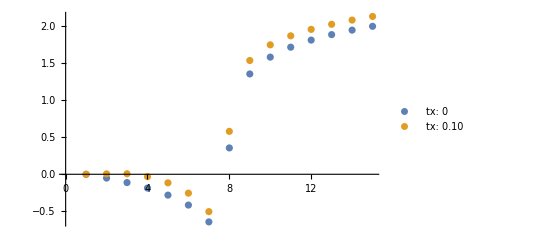

```mathematica
ListPlot[txtablesum, PlotLegends->Map["tx: "<>ToString[DecimalForm[#, {2,2}]]&,  txlist]]
```

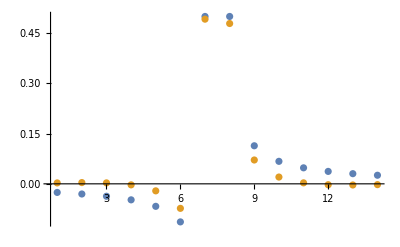

```mathematica
ListPlot[Table[integratedtxtable[[;;,i, i+1]], {i, 2 numterms}]//Transpose, PlotRange->All]
```

```mathematica
Table[integratedtxtable[[;;,i, i+1]], {i, 2 numterms}]//Transpose
```

{{-0.0256714,-0.0303533,-0.037129,-0.0478151,-0.0672094,-0.113706,0.5,0.5,0.113706,0.0672094,0.0478151,0.037129,0.0303533,0.0256714},{0.00273955,0.0037464,0.00286216,-0.0030445,-0.0209584,-0.0732282,0.491908,0.478936,0.0712207,0.0202951,0.00294907,-0.00268144,-0.00344498,-0.00241112}}

# Lots of mess

```mathematica
Table[Total[Flatten[Take[integratedmntable, i,i]]],{i, Dimensions[integratedmntable][[1]]}]
```

{0,-1.,-1.22741,-1.36183,-1.45746,-1.53172,-1.59242,-1.64377,-1.68825,-1.72749}

```mathematica
integratedtxtable=NIntegrate[txtable/.tz->0, {kappa, -Infinity, Infinity}];
integratedtxtable[[;;,1,1]]=0;
```

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kappa near {kappa} = {-8.14416}. NIntegrate obtained -0.10752 and 0.0000447418 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kappa near {kappa} = {-10.1324}. NIntegrate obtained -0.0347039 and 1.0044×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kappa near {kappa} = {-11.4902}. NIntegrate obtained -0.017214 and 1.79238×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

```mathematica
Table[
Table[Total[Flatten[Take[integratedtxtable[[txindex]], i,i]]],{i, Dimensions[integratedmntable[[txindex]]][[1]]}],
{txindex, Length[integratedtxtable]}
]
```

{{0,-1.,-1.22741,-1.36183,-1.45746,-1.53172,-1.59242,-1.64377,-1.68825,-1.72749},{0,-1.11905,-1.48181,-1.74046,-1.98433,-2.22513,-2.45293,-2.66545,-2.86299,-3.05289},{0,-1.22384,-1.95864,-2.56561,-3.07541,-3.58636,-4.03781,-4.50732,-4.94085,-5.38368},{0,-1.06383,-2.61396,-4.00199,-5.12394,-6.24993,-7.39343,-8.47977,-9.58122,-10.7296}}

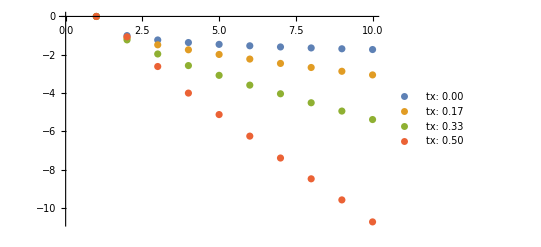

```mathematica
ListPlot[%, PlotLegends->Map["tx: "<>ToString[DecimalForm[#, {2,2}]]&,  txlist]]
```

```mathematica
NIntegrate[mntable/.tz->0/.tx->0.4, {kappa, -Infinity, Infinity}];
```

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kappa near {kappa} = {-3.09626}. NIntegrate obtained -0.281692 and 0.0000221562 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kappa near {kappa} = {-3.7854}. NIntegrate obtained -0.179141 and 3.90297×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kappa near {kappa} = {-4.33378}. NIntegrate obtained -0.120587 and 1.27549×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

```mathematica
%//TableForm
```

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate[Indeterminate,{kappa,-∞,∞}] | -0.378734 | -0.281692 | -0.179141 | -0.120587 | -0.0866549 | -0.0658894 | -0.0524296 | -0.0432308 | -0.0366453
-0.378734 | -0.445945 | -0.221128 | -0.100739 | -0.0497131 | -0.0350121 | -0.0339957 | -0.0361512 | -0.0377485 | -0.0380019
-0.247632 | -0.274369 | -0.0456048 | -0.0283776 | -0.0644409 | -0.0824703 | -0.0765277 | -0.0591817 | -0.0410131 | -0.0403383
-0.154341 | -0.14745 | -0.0468801 | -0.0935982 | -0.089705 | -0.0505568 | -0.0220081 | -0.0319566 | -0.0242227 | -0.0340518
-0.104249 | -0.0900842 | -0.0896027 | -0.0966632 | -0.0413722 | -0.0166765 | -0.0279025 | -0.0412536 | -0.0395234 | -0.0285091
-0.0757185 | -0.0717785 | -0.105853 | -0.0598067 | -0.0244536 | -0.0419757 | -0.053036 | -0.0381518 | -0.018945 | -0.0218977
-0.0582829 | -0.0669958 | -0.0958422 | -0.0436915 | -0.0418656 | -0.0564159 | -0.035991 | -0.0162153 | -0.0183523 | -0.0286712
-0.0469223 | -0.0649869 | -0.075976 | -0.0311626 | -0.058223 | -0.0419575 | -0.0189015 | -0.0236312 | -0.0353909 | -0.0316408
-0.0390943 | -0.0624253 | -0.0685852 | -0.0389413 | -0.0573076 | -0.0253359 | -0.0237 | -0.0369658 | -0.0310959 | -0.0163348
-0.0334384 | -0.0588923 | -0.0448706 | -0.0483154 | -0.0396099 | -0.0212629 | -0.0360293 | -0.0338761 | -0.0174662 | -0.0153953

```mathematica
tx0values=MapThread[Flatten[{#1, #2}]&, {Flatten[%144], Flatten[Table[{m,n},{m,0,10},{n,-1, -12,-1}], 1]}];
```

MapThread::mptd: Object %144 at position {2, 1} in MapThread[Flatten[{#1,#2}]&,{%144,{{0,-1},{0,-2},{0,-3},{0,-4},{0,-5},{0,-6},{0,-7},{0,-8},{0,-9},{0,-10},«122»}}] has only 0 of required 1 dimensions.

```mathematica
Export[FileNameJoin[{NotebookDirectory[], "tx0.csv"}], tx0values]
```

MapThread::mptd: Object %144 at position {2, 1} in MapThread[Flatten[{#1,#2}]&,{%144,{{0,-1},{0,-2},{0,-3},{0,-4},{0,-5},{0,-6},{0,-7},{0,-8},{0,-9},{0,-10},«122»}}] has only 0 of required 1 dimensions.

/home/thorvald/Documents/NTNU/10semester/mathematica/tx0.csv

```mathematica
tx01values=MapThread[Flatten[{#1, #2}]&, {Flatten[%166], Flatten[Table[{m,n},{m,0,10},{n,-1, -12,-1}], 1]}];
```

MapThread::mptd: Object %166 at position {2, 1} in MapThread[Flatten[{#1,#2}]&,{%166,{{0,-1},{0,-2},{0,-3},{0,-4},{0,-5},{0,-6},{0,-7},{0,-8},{0,-9},{0,-10},«122»}}] has only 0 of required 1 dimensions.

```mathematica
Export[FileNameJoin[{NotebookDirectory[], "tx0.1.csv"}], tx01values]
```

MapThread::mptd: Object %166 at position {2, 1} in MapThread[Flatten[{#1,#2}]&,{%166,{{0,-1},{0,-2},{0,-3},{0,-4},{0,-5},{0,-6},{0,-7},{0,-8},{0,-9},{0,-10},«122»}}] has only 0 of required 1 dimensions.

/home/thorvald/Documents/NTNU/10semester/mathematica/tx0.1.csv

```mathematica
tx04values=MapThread[Flatten[{#1, #2}]&, {Flatten[%175], Flatten[Table[{m,n},{m,0,10},{n,-1, -12,-1}], 1]}];
```

MapThread::mptd: Object %175 at position {2, 1} in MapThread[Flatten[{#1,#2}]&,{%175,{{0,-1},{0,-2},{0,-3},{0,-4},{0,-5},{0,-6},{0,-7},{0,-8},{0,-9},{0,-10},«122»}}] has only 0 of required 1 dimensions.

```mathematica
Export[FileNameJoin[{NotebookDirectory[], "tx0.4.csv"}], tx01values]
```

MapThread::mptd: Object %166 at position {2, 1} in MapThread[Flatten[{#1,#2}]&,{%166,{{0,-1},{0,-2},{0,-3},{0,-4},{0,-5},{0,-6},{0,-7},{0,-8},{0,-9},{0,-10},«122»}}] has only 0 of required 1 dimensions.

/home/thorvald/Documents/NTNU/10semester/mathematica/tx0.4.csv

```mathematica
Flatten[Table[{m,n},{m,0,10},{n,-1, -12,-1}], 1]
```

{{0,-1},{0,-2},{0,-3},{0,-4},{0,-5},{0,-6},{0,-7},{0,-8},{0,-9},{0,-10},{0,-11},{0,-12},{1,-1},{1,-2},{1,-3},{1,-4},{1,-5},{1,-6},{1,-7},{1,-8},{1,-9},{1,-10},{1,-11},{1,-12},{2,-1},{2,-2},{2,-3},{2,-4},{2,-5},{2,-6},{2,-7},{2,-8},{2,-9},{2,-10},{2,-11},{2,-12},{3,-1},{3,-2},{3,-3},{3,-4},{3,-5},{3,-6},{3,-7},{3,-8},{3,-9},{3,-10},{3,-11},{3,-12},{4,-1},{4,-2},{4,-3},{4,-4},{4,-5},{4,-6},{4,-7},{4,-8},{4,-9},{4,-10},{4,-11},{4,-12},{5,-1},{5,-2},{5,-3},{5,-4},{5,-5},{5,-6},{5,-7},{5,-8},{5,-9},{5,-10},{5,-11},{5,-12},{6,-1},{6,-2},{6,-3},{6,-4},{6,-5},{6,-6},{6,-7},{6,-8},{6,-9},{6,-10},{6,-11},{6,-12},{7,-1},{7,-2},{7,-3},{7,-4},{7,-5},{7,-6},{7,-7},{7,-8},{7,-9},{7,-10},{7,-11},{7,-12},{8,-1},{8,-2},{8,-3},{8,-4},{8,-5},{8,-6},{8,-7},{8,-8},{8,-9},{8,-10},{8,-11},{8,-12},{9,-1},{9,-2},{9,-3},{9,-4},{9,-5},{9,-6},{9,-7},{9,-8},{9,-9},{9,-10},{9,-11},{9,-12},{10,-1},{10,-2},{10,-3},{10,-4},{10,-5},{10,-6},{10,-7},{10,-8},{10,-9},{10,-10},{10,-11},{10,-12}}

```mathematica
MatrixPlot[integratedmntable, PlotLegends->Automatic]
```

-Graphics-

```mathematica
MatrixPlot[Transpose[%], PlotLegends->Automatic]
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Function::slot: Slot[«1»] (in Blend[System`PlotThemeDump`$ThemeDefaultMatrix,Slot[«1»]]&) should contain a non-negative integer or string.

MatrixPlot::mat0: Argument … at position 1 is not a matrix.

MatrixPlot[Transpose[-Graphics-],PlotLegends→Automatic]

```mathematica
Table[Total[Flatten[Take[%111, i,i]]],{i, 11}]
```

Take::take: Cannot take positions 1 through 1 in 111.

Take::take: Cannot take positions 1 through 2 in %111.

Take::take: Cannot take positions 1 through 3 in %111.

General::stop: Further output of Take::take will be suppressed during this calculation.

{Total[Take[%111,1,1]],Total[Take[%111,2,2]],Total[Take[%111,3,3]],Total[Take[%111,4,4]],Total[Take[%111,5,5]],Total[Take[%111,6,6]],Total[Take[%111,7,7]],Total[Take[%111,8,8]],Total[Take[%111,9,9]],Total[Take[%111,10,10]],Total[Take[%111,11,11]]}

```mathematica
Differences[%128]
```

Differences[%128]

```mathematica
MatrixPlot[Transpose[PadLeft[%23]], PlotLegends->Automatic]
```

MatrixPlot::mat0: Argument {-1.,-0.227411,-0.134419,-0.0956303,-0.0742579,-0.0607066,-0.0513429,-0.044484,-0.0392429} at position 1 is not a matrix.

MatrixPlot[{-1.,-0.227411,-0.134419,-0.0956303,-0.0742579,-0.0607066,-0.0513429,-0.044484,-0.0392429},PlotLegends→Automatic]

```mathematica
MatrixPlot[
Drop[
LowerTriangularize[Transpose[PadLeft[%23]], -1],
1, -2]
]
```

LowerTriangularize::matrix: Argument {-1.,-0.227411,-0.134419,-0.0956303,-0.0742579,-0.0607066,-0.0513429,-0.044484,-0.0392429} at position 1 is not a non-empty rectangular matrix.

Drop::drop: Cannot drop positions -2 through -1 in -1.

MatrixPlot::mat0: Argument Drop[LowerTriangularize[{-1.,-0.227411,-0.134419,-0.0956303,-0.0742579,-0.0607066,-0.0513429,-0.044484,-0.0392429},-1],1,-2] at position 1 is not a matrix.

MatrixPlot[Drop[LowerTriangularize[{-1.,-0.227411,-0.134419,-0.0956303,-0.0742579,-0.0607066,-0.0513429,-0.044484,-0.0392429},-1],1,-2]]

```mathematica
MatrixPlot[Transpose[PadRight[%86]], PlotLegends->Automatic]
```

MatrixPlot::mat0: Argument Transpose[PadRight[%86]] at position 1 is not a matrix.

MatrixPlot[Transpose[PadRight[%86]],PlotLegends→Automatic]

```mathematica
MatrixPlot[%]
```

MatrixPlot::mat0: Argument Transpose[PadRight[%86]] at position 1 is not a matrix.

MatrixPlot::mat0: Argument MatrixPlot[Transpose[PadRight[%86]],PlotLegends→Automatic] at position 1 is not a matrix.

MatrixPlot[MatrixPlot[Transpose[PadRight[%86]],PlotLegends→Automatic]]

```mathematica
%
```

MatrixPlot::mat0: Argument Transpose[PadRight[%86]] at position 1 is not a matrix.

MatrixPlot::mat0: Argument MatrixPlot[Transpose[PadRight[%86]],PlotLegends→Automatic] at position 1 is not a matrix.

MatrixPlot[MatrixPlot[Transpose[PadRight[%86]],PlotLegends→Automatic]]

```mathematica
MatrixPlot[%113, PlotLegends->Automatic]
```

MatrixPlot::mat0: Argument %113 at position 1 is not a matrix.

MatrixPlot[%113,PlotLegends→Automatic]

```mathematica
Total[%, {2}]Ξ2/.N->N-1, M->M-1)
```

```mathematica
Ξ2/.N->N-1, M->M-1)
```

```mathematica
ListPlot[-Accumulate[%]*4]
```

MatrixPlot::mat0: Argument %113 at position 1 is not a matrix.

ListPlot::lpn: -4. MatrixPlot[%113,%113+(PlotLegends→Automatic)] is not a list of numbers or pairs of numbers.

ListPlot[-4 MatrixPlot[%113,%113+(PlotLegends→Automatic)]]

```mathematica
ListPlot[-Accumulate[%]*4]
```

MatrixPlot::argt: MatrixPlot called with 2 arguments; 0 or 1 arguments are expected.

ListPlot::lpn: -4. MatrixPlot[%113,%113+(PlotLegends→Automatic)] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[-4 ListPlot[-4 MatrixPlot[%113,%113+(PlotLegends→Automatic)]]]

```mathematica
MatrixPlot[PadLeft[%]]
```

MatrixPlot::argt: MatrixPlot called with 2 arguments; 0 or 1 arguments are expected.

ListPlot::lpn: -4. MatrixPlot[%113,%113+(PlotLegends→Automatic)] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

MatrixPlot::mat0: Argument PadLeft[ListPlot[-4 ListPlot[-4 MatrixPlot[%113,Out[«1»]+Rule[«2»]]]]] at position 1 is not a matrix.

MatrixPlot[PadLeft[ListPlot[-4 ListPlot[-4 MatrixPlot[%113,%113+(PlotLegends→Automatic)]]]]]

```mathematica
MatrixPlot[%]
```

MatrixPlot::argt: MatrixPlot called with 2 arguments; 0 or 1 arguments are expected.

ListPlot::lpn: -4. MatrixPlot[%113,%113+(PlotLegends→Automatic)] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

$Aborted